```mathematica
γ[E_]=(511+E)/511;
β[E_]=Sqrt[(γ[E]^2-1)/γ[E]^2];
Acosta[θ_,β_,A_,B_]=Module[{x1,x2,bp},bp=(1+B)β; x1=((Cos[θ]-bp)/(1-bp Cos[θ]))^2;x2=(1-bp^2)/((1-bp Cos[θ])^2);((3 A/8)(1+x1)+(4(1-A)/3)(1-x1))x2/((2/9)(16-7A)π)];
```

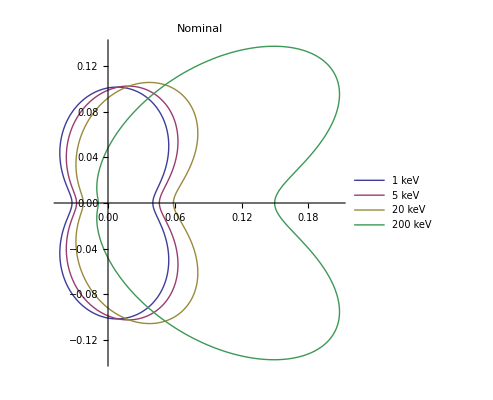

```mathematica
PolarPlot[{Acosta[θ, β[1.0],0.435048, -0.120482],Acosta[θ, β[5.0],0.435048, -0.120482],Acosta[θ, β[20.0],0.435048, -0.120482],Acosta[θ, β[200.0],0.435048, -0.120482]},{θ,-π,π},PlotLabel->"Nominal",PlotLegends-> {"1 keV","5 keV", "20 keV", "200 keV"},DisplayFunction->Identity]
```